(C3 (ⅇ^(Beta1 Ener1) (Ener1+Ener2)+C1 Ener2 PA)+ⅇ^(Beta1 Ener3) (-ⅇ^(Beta1 Ener1) (Ener1+Ener2-Ener3)+C1 (-Ener2+Ener3) PA) PB)/((ⅇ^(Beta1 Ener1)+C1 PA) (C3-ⅇ^(Beta1 Ener3) PB))

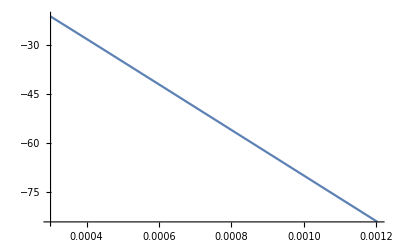

(ⅇ^(-Beta1 Ener2) (1.-0.0001 ⅇ^(Beta1 Ener3)))/(1.+ⅇ^(Beta1 Ener1))

(ⅇ^(-70000 Beta1) (1-ⅇ^(-10000 Beta1)))/(1+ⅇ^(-10000 Beta1))

Log[(ⅇ^(-70000 Beta1) (1-ⅇ^(-10000 Beta1)))/(1+ⅇ^(-10000 Beta1))]

-(10000 (-7-2 ⅇ^(10000 Beta1)+7 ⅇ^(20000 Beta1)))/(-1+ⅇ^(20000 Beta1))

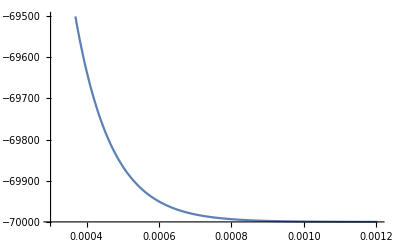

(ⅇ^(-60000 Beta1-Beta1 Ener1) (1-ⅇ^(-10000 Beta1)))/(1+ⅇ^(-Beta1 Ener1))

(0.96023 ⅇ^(-19.3478-0.000322464 Ener1))/(1+ⅇ^(-0.000322464 Ener1))

#diffrate

1/((1+ⅇ^(0.000322464 Ener1))^2)1.57362×10^-10 (-1.43867×10^6-ⅇ^(0.000322464 (10000+Ener1)) (60000+Ener1)+ⅇ^(0.000322464 Ener1) (70000+Ener1))

-(-10000+Ener1) (-5000+Ener1)

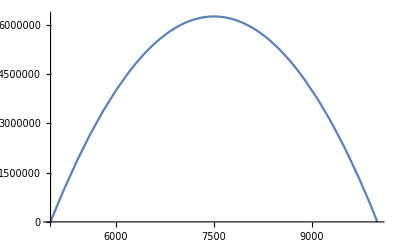

1.42111

41988.7

```mathematica
Clear[Beta1,C1,C2,C3,PA,PB]
Eq1[Ener1_,Beta1_,C1_] := C1*Exp[-Beta1*Ener1]
Rate2[Ener2_,Beta1_,C2_] := C2*Exp[-Beta1*Ener2]
Eq3[Ener3_,Beta1_,C3_] := C3*Exp[-Beta1*Ener3]
RateTotal[Ener1_,Ener2_,Ener3_,Beta1_,PA_,PB_,C1_,C2_,C3_] = Rate2[Ener2,Beta1,C2]*Eq1[Ener1,Beta1,C1]*PA*(1-PB/(Eq3[Ener3,Beta1,C3]))/(1+Eq1[Ener1,Beta1,C1]*PA);
(*RateT[Ener1_,Ener2_,Ener3_] = Rate2*Eq1*PA*(1-PB/Eq3)/(1+Eq1*PA)*)

Simplify[D[-Log[RateTotal[Ener1,Ener2,Ener3,Beta1,PA,PB,C1,C2,C3]],Beta1]]
(*(*Plot of lnrate/dbeta*)
Plot[RateTotal[10000,60000,-10000,Beta1,1,0.0001,1,1,1],{Beta1,0.00030069761,0.00120279047}]*)

(*Plot of lnrate/dbeta*)
Plot[Log[RateTotal[10000,60000,-10000,Beta1,1,1,1,1,1]],{Beta1,0.00030069761,0.00120279047}]

(*Plot of -dlnrate/dbeta*)
rate = Simplify[RateTotal[Ener1,Ener2,Ener3,Beta1,1,0.0001,1,1,1]]
rate = RateTotal[10000,60000,-10000,Beta1,1,1,1,1,1]
lograte = Log[rate]
diffrate = Simplify[D[lograte,Beta1]]
Plot[diffrate,{Beta1,0.00030069761,0.00120279047}]
rate = RateTotal[Ener1,60000,-10000,Beta1,1,1,1,1,1]
rate1 =RateTotal[Ener1,60000,-10000,Beta1,1,1,1,1,1]/.Beta1->(1/(8.314*373))
#diffrate
diffrate1 = Simplify[D[rate,Beta1]]/.Beta1->(1/(8.314*373))
dist1 = -1*(Ener1-5000)*(Ener1-10000)
(*dist1 = PDF[NormalDistribution[10000,2500],Ener1]*)
Plot[dist1,{Ener1,5000,15000},PlotRange->{{5000,10000},{0,6250000}}]
avgrate = N[Integrate[dist1*rate1,{Ener1,5000,15000}]]
numer1 = N[Integrate[dist1*(D[rate,Beta1]/.Beta1->(1/(8.314*373))),{Ener1,5000,15000}]];
denom1 = avgrate;
avgEw = -numer1/denom1



(*(*Plot of -dlnrate2/d2beta ---- SECOND DERIVATIVE*)
Plot[D[Log[RateTotal[10000,60000,-10000,Beta1,1,0.0001,1,1,1],{Beta1,2}]],{Beta1,0.00030069761,0.00120279047}]*)
```